## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= λt*D[yt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-D[xt*P[xt, yt],yt]+(αt^2/2)D[P[xt, yt],{xt,2}]+(αt^2/2)D[P[xt, yt],{yt,2}]
```

P[xt,yt]-xt P^(0,1)[xt,yt]+yt P^(0,1)[xt,yt]+1/2 αt^2 P^(0,2)[xt,yt]+yt λt P^(1,0)[xt,yt]+1/2 αt^2 P^(2,0)[xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{αt,0},{0,αt}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{αt,0},{0,αt}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{αt^2/2+αt^2/(2 λt)+(αt^2 λt)/2,αt^2/(2 λt)},{αt^2/(2 λt),αt^2/2+αt^2/(2 λt)}}

## Choose the parameter values

```mathematica
λts = {0.02,0.05, 0.1, 0.15,0.24};
αts = {0.05, 0.1, 0.2, 0.5, 1.0};
tfs = Flatten[Transpose[Table[5/λts, 5]]]
αArray2 = Flatten[Table[{0.3, 0.4, 0.5, 0.6, 0.7},5]]^2
params = Flatten[Table[{λt->l, αt->a}, {l, λts}, {a, αts}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αt="<>ToString[a], {l, λts},{a, αts}], 1];
```

{250.,250.,250.,250.,250.,100.,100.,100.,100.,100.,50.,50.,50.,50.,50.,33.3333,33.3333,33.3333,33.3333,33.3333,20.8333,20.8333,20.8333,20.8333,20.8333}

{0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49,0.09,0.16,0.25,0.36,0.49}

{{λt→0.02,αt→0.3},{λt→0.02,αt→0.4},{λt→0.02,αt→0.5},{λt→0.02,αt→0.6},{λt→0.02,αt→0.7},{λt→0.05,αt→0.3},{λt→0.05,αt→0.4},{λt→0.05,αt→0.5},{λt→0.05,αt→0.6},{λt→0.05,αt→0.7},{λt→0.1,αt→0.3},{λt→0.1,αt→0.4},{λt→0.1,αt→0.5},{λt→0.1,αt→0.6},{λt→0.1,αt→0.7},{λt→0.15,αt→0.3},{λt→0.15,αt→0.4},{λt→0.15,αt→0.5},{λt→0.15,αt→0.6},{λt→0.15,αt→0.7},{λt→0.24,αt→0.3},{λt→0.24,αt→0.4},{λt→0.24,αt→0.5},{λt→0.24,αt→0.6},{λt→0.24,αt→0.7}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cstar =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.02084,1.02084,1.02084,1.02084,1.02084,1.05573,1.05573,1.05573,1.05573,1.05573,1.12702,1.12702,1.12702,1.12702,1.12702,1.22515,1.22515,1.22515,1.22515,1.22515,1.66667,1.66667,1.66667,1.66667,1.66667}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
```

{1.51522,2.0203,2.52537,3.03045,3.53552,0.973268,1.29769,1.62211,1.94654,2.27096,0.706753,0.942338,1.17792,1.41351,1.64909,0.593085,0.79078,0.988475,1.18617,1.38387,0.493254,0.657673,0.822091,0.986509,1.15093}

{1.51493,2.0199,2.52488,3.02985,3.53483,0.972111,1.29615,1.62019,1.94422,2.26826,0.703562,0.938083,1.1726,1.40712,1.64165,0.587367,0.783156,0.978945,1.17473,1.37052,0.482183,0.64291,0.803638,0.964365,1.12509}

```mathematica
deltaWidth = 0.2;
deltaVar = deltaWidth^2
minCell = deltaWidth/4
```

0.04

0.05

```mathematica
Sqrt[0.05]
```

0.223607

```mathematica
Sqrt[αts[[1]]^2/2]
```

0.212132

#### Boundary condition at x~* =1. Choose the boundaries to be far enough away from the initial condition and the final distribution

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
xt0 = 12;
yt0 = xt0*cstar;
xtls=1-5*Sqrt[αArray2]
xtrs = xt0+5*xtStds
ytls=cstar
ytrs = cstar*xt0+5*ytStds
```

{-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5,-0.5,-1.,-1.5,-2.,-2.5}

{19.5761,22.1015,24.6269,27.1522,29.6776,16.8663,18.4885,20.1106,21.7327,23.3548,15.5338,16.7117,17.8896,19.0675,20.2455,14.9654,15.9539,16.9424,17.9309,18.9193,14.4663,15.2884,16.1105,16.9325,17.7546}

{1.02084,1.02084,1.02084,1.02084,1.02084,1.05573,1.05573,1.05573,1.05573,1.05573,1.12702,1.12702,1.12702,1.12702,1.12702,1.22515,1.22515,1.22515,1.22515,1.22515,1.66667,1.66667,1.66667,1.66667,1.66667}

{19.8247,22.3496,24.8745,27.3994,29.9242,17.5293,19.1495,20.7697,22.3898,24.01,17.042,18.2146,19.3872,20.5598,21.7324,17.6386,18.6176,19.5965,20.5754,21.5544,22.4109,23.2146,24.0182,24.8218,25.6255}

{{12,12.2501},{12,12.2501},{12,12.2501},{12,12.2501},{12,12.2501},{12,12.6687},{12,12.6687},{12,12.6687},{12,12.6687},{12,12.6687},{12,13.5242},{12,13.5242},{12,13.5242},{12,13.5242},{12,13.5242},{12,14.7018},{12,14.7018},{12,14.7018},{12,14.7018},{12,14.7018},{12,20.},{12,20.},{12,20.},{12,20.},{12,20.}}

{{0.04,0},{0,0.04}}

{{0.2,0},{0,0.2}}

{ImplicitRegion[-0.5≤xt≤19.5761&&1.02084≤yt≤19.8247,{xt,yt}],ImplicitRegion[-1.≤xt≤22.1015&&1.02084≤yt≤22.3496,{xt,yt}],ImplicitRegion[-1.5≤xt≤24.6269&&1.02084≤yt≤24.8745,{xt,yt}],ImplicitRegion[-2.≤xt≤27.1522&&1.02084≤yt≤27.3994,{xt,yt}],ImplicitRegion[-2.5≤xt≤29.6776&&1.02084≤yt≤29.9242,{xt,yt}],ImplicitRegion[-0.5≤xt≤16.8663&&1.05573≤yt≤17.5293,{xt,yt}],ImplicitRegion[-1.≤xt≤18.4885&&1.05573≤yt≤19.1495,{xt,yt}],ImplicitRegion[-1.5≤xt≤20.1106&&1.05573≤yt≤20.7697,{xt,yt}],ImplicitRegion[-2.≤xt≤21.7327&&1.05573≤yt≤22.3898,{xt,yt}],ImplicitRegion[-2.5≤xt≤23.3548&&1.05573≤yt≤24.01,{xt,yt}],ImplicitRegion[-0.5≤xt≤15.5338&&1.12702≤yt≤17.042,{xt,yt}],ImplicitRegion[-1.≤xt≤16.7117&&1.12702≤yt≤18.2146,{xt,yt}],ImplicitRegion[-1.5≤xt≤17.8896&&1.12702≤yt≤19.3872,{xt,yt}],ImplicitRegion[-2.≤xt≤19.0675&&1.12702≤yt≤20.5598,{xt,yt}],ImplicitRegion[-2.5≤xt≤20.2455&&1.12702≤yt≤21.7324,{xt,yt}],ImplicitRegion[-0.5≤xt≤14.9654&&1.22515≤yt≤17.6386,{xt,yt}],ImplicitRegion[-1.≤xt≤15.9539&&1.22515≤yt≤18.6176,{xt,yt}],ImplicitRegion[-1.5≤xt≤16.9424&&1.22515≤yt≤19.5965,{xt,yt}],ImplicitRegion[-2.≤xt≤17.9309&&1.22515≤yt≤20.5754,{xt,yt}],ImplicitRegion[-2.5≤xt≤18.9193&&1.22515≤yt≤21.5544,{xt,yt}],ImplicitRegion[-0.5≤xt≤14.4663&&1.66667≤yt≤22.4109,{xt,yt}],ImplicitRegion[-1.≤xt≤15.2884&&1.66667≤yt≤23.2146,{xt,yt}],ImplicitRegion[-1.5≤xt≤16.1105&&1.66667≤yt≤24.0182,{xt,yt}],ImplicitRegion[-2.≤xt≤16.9325&&1.66667≤yt≤24.8218,{xt,yt}],ImplicitRegion[-2.5≤xt≤17.7546&&1.66667≤yt≤25.6255,{xt,yt}]}

{ElementMesh[{{-0.5,19.5761},{1.02084,19.8247}},{TriangleElement[<46320>]}],ElementMesh[{{-1.,22.1015},{1.02084,22.3496}},{TriangleElement[<54730>]}],ElementMesh[{{-1.5,24.6269},{1.02084,24.8745}},{TriangleElement[<64024>]}],ElementMesh[{{-2.,27.1522},{1.02084,27.3994}},{TriangleElement[<73556>]}],ElementMesh[{{-2.5,29.6776},{1.02084,29.9242}},{TriangleElement[<83560>]}],ElementMesh[{{-0.5,16.8663},{1.05573,17.5293}},{TriangleElement[<38782>]}],ElementMesh[{{-1.,18.4885},{1.05573,19.1495}},{TriangleElement[<44396>]}],ElementMesh[{{-1.5,20.1106},{1.05573,20.7697}},{TriangleElement[<49990>]}],ElementMesh[{{-2.,21.7327},{1.05573,22.3898}},{TriangleElement[<55768>]}],ElementMesh[{{-2.5,23.3548},{1.05573,24.01}},{TriangleElement[<62010>]}],ElementMesh[{{-0.5,15.5338},{1.12702,17.042}},{TriangleElement[<36434>]}],ElementMesh[{{-1.,16.7117},{1.12702,18.2146}},{TriangleElement[<40356>]}],ElementMesh[{{-1.5,17.8896},{1.12702,19.3872}},{TriangleElement[<44502>]}],ElementMesh[{{-2.,19.0675},{1.12702,20.5598}},{TriangleElement[<48620>]}],ElementMesh[{{-2.5,20.2455},{1.12702,21.7324}},{TriangleElement[<53230>]}],ElementMesh[{{-0.5,14.9654},{1.22515,17.6386}},{TriangleElement[<36008>]}],ElementMesh[{{-1.,15.9539},{1.22515,18.6176}},{TriangleElement[<39392>]}],ElementMesh[{{-1.5,16.9424},{1.22515,19.5965}},{TriangleElement[<43080>]}],ElementMesh[{{-2.,17.9309},{1.22515,20.5754}},{TriangleElement[<46952>]}],ElementMesh[{{-2.5,18.9193},{1.22515,21.5544}},{TriangleElement[<50510>]}],ElementMesh[{{-0.5,14.4663},{1.66667,22.4109}},{TriangleElement[<41360>]}],ElementMesh[{{-1.,15.2884},{1.66667,23.2146}},{TriangleElement[<44436>]}],ElementMesh[{{-1.5,16.1105},{1.66667,24.0182}},{TriangleElement[<47792>]}],ElementMesh[{{-2.,16.9325},{1.66667,24.8218}},{TriangleElement[<51008>]}],ElementMesh[{{-2.5,17.7546},{1.66667,25.6255}},{TriangleElement[<54488>]}]}

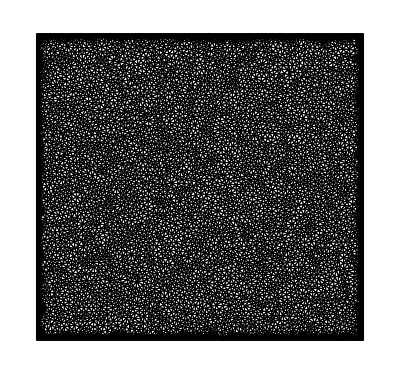

```mathematica
icPos =Transpose[{Table[xt0, 25], yt0}]
icVar ={{deltaVar, 0},{0, deltaVar}}
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {xt, yt}], {pos, icPos}]];
Sqrt[icVar]
bcFunc[xtl_, xtr_, ytl_, ytr_] :={
	  P[xtl, yt]==0,
           P[xtr, yt]==0,
           P[xt, ytr]==0,
           P[xt, ytl]==0
};
ΩFunc[xtl_, xtr_, ytl_, ytr_] :=ImplicitRegion[True,{{xt,xtl,xtr},{yt,ytl,ytr}}];
bcs = MapThread[bcFunc, {xtls, xtrs, ytls, ytrs}];
Ω=MapThread[ΩFunc,{xtls, xtrs, ytls, ytrs}]
meshes = Table[ToElementMesh[o, MaxCellMeasure->minCell, MaxBoundaryCellMeasure->minCell/4], {o, Ω}]
meshes[[1]]["Wireframe"]
```

General::munfl: 1/2.71828^1024.96 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

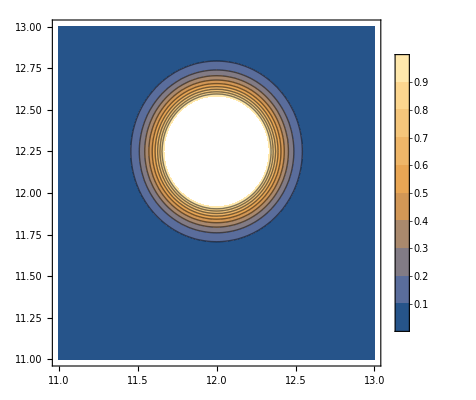

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt, xt0-1, xt0+1}, {yt, xt0-1, xt0+1}, PlotRange->{0,1}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement"}];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

```mathematica
dv = Table[Derivative[0,1][sol], {sol, solsIc0}];
```

```mathematica
Plot3D[solsIc0[[1]][xt, yt], {xt, 0,xtrs[[1]]}, {yt, 0,ytrs[[1]]}, AxesLabel->{xt, yt}, PlotRange->{-0.01, 50}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{dv,ytls}])*(αArray2/2);
```

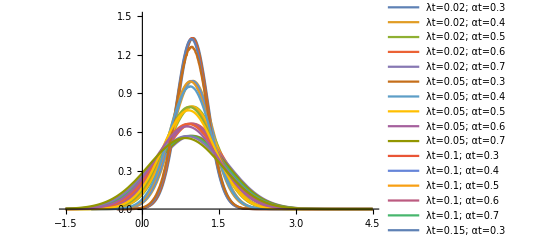

```mathematica
Plot[XIc0, {xt, -1.5, 4.5}, PlotLegends->legend, PlotRange->{-0.1, 1.5}]
```

```mathematica
XIc0[[1]][[2]][[0]][[1]][[1]]
```

{-0.5,19.5761}

```mathematica
bounds = Table[{y[[2]][[0]][[1]][[1]][[1]],3}, {y, XIc0}]
```

{{-0.5,3},{-1.,3},{-1.5,3},{-2.,3},{-2.5,3},{-0.5,3},{-1.,3},{-1.5,3},{-2.,3},{-2.5,3},{-0.5,3},{-1.,3},{-1.5,3},{-2.,3},{-2.5,3},{-0.5,3},{-1.,3},{-1.5,3},{-2.,3},{-2.5,3},{-0.5,3},{-1.,3},{-1.5,3},{-2.,3},{-2.5,3}}

```mathematica
IntegFunc[f_, bound_] :=NIntegrate[f, {xt, bound[[1]], bound[[2]]}]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0,bounds}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*xt,bounds}]
secondIc0 = MapThread[IntegFunc, {corrected*xt*xt,bounds}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.976508}. NIntegrate obtained 1.00009 and 0.0000385275 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.1015}. NIntegrate obtained 1.00005 and 0.000021601 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.12786}. NIntegrate obtained 0.999932 and 0.0000183211 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{1.00009,1.00005,0.999932,0.999599,0.998015,0.999913,0.999987,0.999968,0.999665,0.998237,0.999712,0.999902,0.999942,0.999705,0.99854,0.999212,0.999679,0.999832,0.9997,0.998707,0.994863,0.998069,0.999098,0.999245,0.998427}

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.976508}. NIntegrate obtained 0.992099 and 0.000030805 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.1015}. NIntegrate obtained 0.98911 and 0.0000221023 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.12786}. NIntegrate obtained 0.986205 and 0.0000188307 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.992099,0.98911,0.986205,0.982626,0.976191,0.981397,0.974191,0.967005,0.95918,0.948901,0.967478,0.953273,0.938954,0.924029,0.906999,0.958664,0.93792,0.916553,0.894447,0.870314,0.961421,0.934157,0.903304,0.869561,0.832368}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.11323}. NIntegrate obtained 1.07381 and 0.0000526347 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.8515}. NIntegrate obtained 1.13821 and 0.0000214246 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {2.07708}. NIntegrate obtained 1.22237 and 0.0000228364 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{1.07381,1.13821,1.22237,1.32383,1.43398,1.05316,1.10898,1.18495,1.27849,1.38246,1.0261,1.06893,1.1319,1.21308,1.30653,1.00967,1.04072,1.09152,1.16103,1.24414,1.02312,1.04633,1.08469,1.13902,1.20616}

{0.0895525,0.159868,0.249773,0.35828,0.481028,0.0900209,0.15993,0.249846,0.35846,0.482043,0.090089,0.160197,0.250261,0.359248,0.483878,0.0906292,0.161031,0.251453,0.360993,0.486698,0.0987941,0.173681,0.268729,0.38288,0.513327}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αts}], 1];
params
```

{{λt→0.02,αt→0.3},{λt→0.02,αt→0.4},{λt→0.02,αt→0.5},{λt→0.02,αt→0.6},{λt→0.02,αt→0.7},{λt→0.05,αt→0.3},{λt→0.05,αt→0.4},{λt→0.05,αt→0.5},{λt→0.05,αt→0.6},{λt→0.05,αt→0.7},{λt→0.1,αt→0.3},{λt→0.1,αt→0.4},{λt→0.1,αt→0.5},{λt→0.1,αt→0.6},{λt→0.1,αt→0.7},{λt→0.15,αt→0.3},{λt→0.15,αt→0.4},{λt→0.15,αt→0.5},{λt→0.15,αt→0.6},{λt→0.15,αt→0.7},{λt→0.24,αt→0.3},{λt→0.24,αt→0.4},{λt→0.24,αt→0.5},{λt→0.24,αt→0.6},{λt→0.24,αt→0.7}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, αts}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[varArrayIc0],5]]
Grid[N[Reverse[normArrayIc0],5]]
```

-Graphics-

0.0987941 | 0.173681 | 0.268729 | 0.38288 | 0.513327
0.0906292 | 0.161031 | 0.251453 | 0.360993 | 0.486698
0.090089 | 0.160197 | 0.250261 | 0.359248 | 0.483878
0.0900209 | 0.15993 | 0.249846 | 0.35846 | 0.482043
0.0895525 | 0.159868 | 0.249773 | 0.35828 | 0.481028

0.994863 | 0.998069 | 0.999098 | 0.999245 | 0.998427
0.999212 | 0.999679 | 0.999832 | 0.9997 | 0.998707
0.999712 | 0.999902 | 0.999942 | 0.999705 | 0.99854
0.999913 | 0.999987 | 0.999968 | 0.999665 | 0.998237
1.00009 | 1.00005 | 0.999932 | 0.999599 | 0.998015

```mathematica
(.0906-.08955)/.08955
```

0.0117253

```mathematica
ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[meanArrayIc0],4]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[meanArrayIc0].

Table::iterb: Iterator {i,Flatten[meanArrayIc0]} does not have appropriate bounds.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[Table[Blend[{{0,Red},{1,White},{5,Blue}},i],{i,Flatten[meanArrayIc0]}],{5,5}].

ArrayPlot::mat: Argument ArrayReshape[Table[Blend[{{0,Red},{1,White},{5,Blue}},i],{i,Flatten[meanArrayIc0]}],{5,5}] at position 1 is not a list of lists.

ArrayPlot[ArrayReshape[Table[Blend[{{0,Red},{1,White},{5,Blue}},i],{i,Flatten[meanArrayIc0]}],{5,5}],PlotLegends→{Placed[,Right]},FrameTicks→{xticks,yticks},DataReversed→True,FrameLabel→{λt,κt}]

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[meanArrayIc0].

Grid[Reverse[meanArrayIc0]]

```mathematica
ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

0.10684 | 0.19885 | 0.329069 | 0.506483 | 0.740216
0.0986043 | 0.183012 | 0.29935 | 0.451421 | 0.642913
0.0962214 | 0.176242 | 0.283852 | 0.420885 | 0.588211
0.0933046 | 0.168513 | 0.267198 | 0.389717 | 0.535392
0.0912139 | 0.163426 | 0.256795 | 0.371112 | 0.504799